# Durin’s Bane

```mathematica
ListAnimate[Import["https://64.media.tumblr.com/70afdbfe8db90de58bbf790c3845e2ea/tumblr_osw9mwY6XW1qfqjxao1_250.gif"]]
```

## Introduction

Hot objects emit light. Balrogs, being fiery demons, produce light.
	
	The Balrog is a fictional monster created by J.R.R. Tolkien, and in the Sindarian language has etymological roots which translate to “demon of might.” Within Tolkien’s writtings, Balrogs make frequent appearances as soldiers and generals within Morgoth’s army. These fire demons are fairly common within the early ages of Middle Earth, but only three detailed personal encounters are given within Tolkien’s legendarium. The first two occur within the unfinished story The Fall of Gondolin. Being among the 	earliest of Tolkien’s writtings, very little description is given of the respective Balrog’s within the story. Gothmog, Lord of the Balrogs, was defeated by Ecthelion of the Fountain, a Lord of Gondolin, who courageously sacrificed himself by impaling the beast with his own helmet, causing both he and the Balrog to fall into a large body of water and drown. The second Balrog, who goes unnamed, was similarly defeated by Glorfindel of Gondolin, in which both fell to their death in a mountainous ravine.
	
	The most detailed battle with a Balrog is given in The Lord of The Rings: The Fellowship of The Ring, in which Gandalf engages in a duel with Durin’s Bane, the Balrog who was awakened by the Dwarves who inhabited the Mines of Moria. From this account, we read directly from the novel:
	
	“It came to the edge of the fire and the light faded as if a cloud had bent over it. [...] The flames roared up to greet it, and wreathed about it; and a black smoke swirled in the air. Its streaming mane kindled, and blazed behind it. In its right hand was a blade like a stabbing tongue of fire; in its left it held a whip of many thongs.”
	
This project intends to deepen understanding of Durin’s Bane, answering 3 questions.

	1. What Temperatures are present on the Balrog?
	2. What is a safe distance from the Balrog?
	3. What are analogies for the Balrog, if they exist?
	
	Hypothesis: The temperature of Durin’s Bane is similar to molten metal or molten rock, enabling close interactions while having just enough energy to stay hot.

## Quantifying Durin’s Bane

An object radiates different wavelengths of light at different temperatures. Because of this, the energy of an object can be calculated by first measuring the wavelengths of light it emits - the hotter the object, the greater the peak wavelength. This Wikipedia article as well as this Youtube video help explain blackbody radiation. A brief mathematical derivation is provided.

## Derived Quantities

Using proportions, we can easily derive the height of the Balrog using Gandalf’s height. Presuming that Sir Ian McKellen is an accurate representation of Gandalf’s height, as he represents him, his height can be used as a scale value which can then easily allow us to derive the dimensions of the Balrog and the distance between the two combatants. Though changing the resolution of the image will change the values, the proportions will remain constant and give us access to more information about Durin’s Bane. Though there will be some discrepancy from actual values due to parallax, the objects in question are relatively close and should be accurate enough to gain insight.

	Doing this analysis provides a height of nearly 4 meters for the Balrog, who may not even be at full posture! Using the Pythagorean Theorem, we can derive the length of the bridge as well. The distance from the Balrog is nearly the Balrog’s height, but still incredibly close for a person to be standing next to a huge heat source.

```mathematica
filmPhoto=Import["https://i.redd.it/uk6pnd9tvxt51.jpg"] (* Offical movie scene, from which we can derive dimensions *)
```

-Graphics-

-Graphics-

```mathematica
GandalfActual=Mean[{178.4,181}]/100 (* Sir Ian McKellen's height as an average of values found online, converted to meters *)
GandalfPhoto=(144-58) (* Using the coordinates reported by Mathematica, we can subtract the y-values to find relative height *);
BalrogPhoto=(318-131);
BalrogActual=(BalrogPhoto/GandalfPhoto)*GandalfActual
BridgePhoto=Sqrt[(393-247)^2+(134-60)^2];
BridgeAcutal=(BridgePhoto/GandalfPhoto)*GandalfActual
```

1.797

3.90743

3.42021

Gandalf is roughly 1.8 meters tall.
	Durin’s Bane is roughly 4 meters tall.
	They are nearly 3.5 meters apart. (The perspective is skewed).

## Blackbody Radiation

A blackbody is an object with perfect absorption of light. In reality, all objects do not have a perfect absorption (100%) of light, but absorb and reflect different amounts depending upon the material. Blackbody calculations are only concerned with the wavelengths of light being emitted and the energy in the object to produce those wavelengths.
	A brief derivation of the math is given.

### Planck’s Law

Wikipedia Article.
	Planck’s radiation law states that the spectral density of electromagnetic radiation in thermal equilibrium at a given temperature T is calculated as follows.

```mathematica
Subscript[B, v][v_,T_] := (2*h*v^3)/c^2*1/(ⅇ^((h*v)/(k*T))-1);
```

This function has constants h, k, and c.
h is Planck’s Constant, 6.626 * 10^-34 joules/Hertz.
k is the Boltzmann Constant, 1.38 * 10^23 joules/Kelvin.
c is the Speed of Light in a Vacuum, 2.99 * 10^8 meters/second.

T is absolute temperature, in Kelvin.
v is the frequency of the electromagnetic radiation, in Hertz.

```mathematica
h=6.62607004*10^-34 (*Planck's Constant*);
k=1.38064852*10^23 (*Boltzmann Constant*);
c=299792460 (*Speed of Light, Vaccuum*);
```

In words, this says “the spectral emittance as a function of light frequency and temperature is the quotient of that frequency’s product with twice Planck’s Constant and the square of the speed of light and the inverse of the difference of the growth constant e raised to the quotient of the product of Planck’s constant with the frequency and Boltzmann’s constant with Temperature.

### Wien’s Displacement Law

Wikipedia Article.
	Wien’s displacement law is derived by maximizing the derivative of a wavelength parameterization of Planck’s law with respect to λ. This law states that the peak wavelength of the light from an object is inversely proportional to the temperature of the object. This is used to find the range of temperatures which are present on the Balrog.

```mathematica
Subscript[λ, Peak] =b/T;
```

```mathematica
b=2.89777196 * 10^-3;
```

b is Wien’s displacement constant, 2.898 * 10^-3 meters*Kelvin.

T is absolute temperature, in Kelvin.

### Stefan-Boltzmann Law

Wikipedia Article.
	The Stefan-Boltzmann law is derived by taking the integral of Planck’s law from 0 to ∞. This law states that the energy per unit surface area  of an object is directly proportional to the fourth power of its temperature and a constant. This is used to find the energy coming from the Balrog, the energy of the thing producing the flames - not the flames themselves.

```mathematica
PwrOut[T_]=σ*T^4;
```

```mathematica
σ=5.67037442 * 10^-8;
```

σ is the Stefan-Boltzmann constant, 5.67 * 10^-8 Watts/(meter^2 Kelvin^4).
T is absolute temperature, in Kelvin.

### Luminosity

Wikipedia Article.
	The luminosity of an object is the same as the Stefan-Boltzmann law, but accounts for the surface area of the object.

```mathematica
Lum[A_]=A*j;
```

A is the surface area of the object, in meters^2.
j is the calculation of the Stefan-Boltzmann law.

This bears much importance to this experiment. Because different surface areas will result in different wattage, the shape of the Balrog must be accounted for.

## 1. What Temperatures are Present on the Balrog?

## Measuring Peak Wavelengths

If Durin’s Bane is a perfect blackbody, then the color of light perceived by its viewers is an average of the wavelengths before and after the peak wavelength. Our looks to us as a giant white-yellow ball, but its peak wavelengths correspond to green light. 

	A note about what follows.
	
	Because the Balrog is fictional, there is no accurate or convenient way to actually measure the peak wavelengths emitted from the creature. The numbers given here are the best guesses made with two sets of human eyes. The images are from different artists and each likely employed different tools and techniques. They are given here for convenience of comprehension, a visual aid.
	A range of is given for each of the three peak wavelengths. Six possible wavelength values are given, and the value used for further calculations is the average between them, with their standard deviations.

#### Wavelengths and the Visible Spectrum

The following two images chart peak wavelengths as a function of intensity. This is used to estimate the values for the wavelengths present on Durin’s Bane. Though the two graphs have different vertical axes, their units are virtually the same. A third image is given which labels the wavelengths of the visible light spectrum, which is used to help estimate peak wavelength values.

```mathematica
maxChart1 =Import["https://sites.google.com/a/coe.edu/courtney-s-chemistry/_/rsrc/1468750973270/home/radical-black-body-radiation/F18-0220Planck20black20body.jpg?height=514&width=924"]

maxChart2=Import["http://howthingswork.org/wp-content/uploads/2017/04/blackbody-radiation-Fig1-768x416.png"]

visiSpectrum=Import["https://www.once.lighting/wp-content/uploads/2020/08/spectrum.png"]
```

-Graphics-

-Graphics-

-Graphics-

#### Lower Wavelength Estimate

This image shows the Balrog in what could be a lower peak wavelength.

```mathematica
lowTempDB=Import["https://pm1.narvii.com/6283/0a7a9f7f6aacca4a5dc56452631eb85a98407ee9_hq.jpg", ImageSize->Medium]
BWlow=Image[Total[lowTempDB//ImageData,{3}]/3]
BWlowData=BWlow//ImageData;
```

-Graphics-

-Graphics-

Based on this image, the lower estimate for peak wavelength is 580 < λ_L < 690.

```mathematica
λL1=597;
λL2=664;
λL3=651;
λL4=625;
λL5=583;
λL6=650;
```

#### Higher Wavelength Estimate

```mathematica
highTempDB=Import["https://pm1.narvii.com/6284/1f54de83b6e7b8dff8f458fced84ecd0afd0dd76_hq.jpg", ImageSize->Medium]
BWhigh=Image[Total[highTempDB//ImageData,{3}]/3]
BWhighData=BWhigh//ImageData;
```

-Graphics-

-Graphics-

Based on this image, the higher estimate for peak wavelength is 530 < λ_L < 640.

```mathematica
λH1=542;
λH2=568;
λH3=533;
λH4=620;
λH5=587;
λH6=602;
```

#### Median Wavelength Estimate

```mathematica
medTempDB=Import["https://i.redd.it/72h95u0l1wb61.jpg", ImageSize->Medium]
BWmed=Image[Total[medTempDB//ImageData,{3}]/3]
BWmedData=BWmed//ImageData;
```

-Graphics-

-Graphics-

Based on this image, the median estimate for peak wavelength is 565 < λ_L < 675.

```mathematica
λM1=583;
λM2=609;
λM3=574;
λM4=570;
λM5=600;
λM6=593;
```

### Peak Wavelength Values

```mathematica
Subscript[λ, L]=(λL1+λL2+λL3+λL4+λL5+λL6) / 6 //N;
Subscript[λ, LDev]=StandardDeviation[{λL1,λL2,λL3,λL4,λL5,λL6}] // N;

Subscript[λ, H]=(λH1+λH2+λH3+λH4+λH5+λH6) / 6 // N;
λHDev=StandardDeviation[{λH1,λH2,λH3,λH4,λH5,λH6}] // N;

Subscript[λ, M]=(λM1+λM2+λM3+λM4+λM5+λM6) / 6 // N;
Subscript[λ, MDev]=StandardDeviation[{λM1,λM2,λM3,λM4,λM5,λM6}] //N;
```

This data was produced by visual guessing. 
	λ_L=628.333 ±  32.5679
	λ_H=575.333 ± 34.0568
	λ_M=588.167 ± 15.1976

#### Analyzing Guess Data

This data possesses high standard deviations, which is to be expected in guess work that has few samples. Before making calculating temperatures, the standard deviation is reduced via iterative computations.

```mathematica
lowList={λL1,λL2,λL3,λL4,λL5,λL6};
highList={λH1,λH2,λH3,λH4,λH5,λH6};
medList={λM1,λM2,λM3,λM4,λM5,λM6};
```

```mathematica
lowMin=628.333-32.5679  //Round;
lowMax=628.333+32.5679 // Round;
highMin=575.333-34.0568 // Round;
highMax=575.333+34.0568 // Round;
medMin=588.167-15.1976 // Round;
medMax=588.167+15.1976 // Round;
```

```mathematica
While[Length[lowList]<50000, AppendTo[lowList,RandomInteger[{lowMin,lowMax}]]];
```

```mathematica
While[Length[highList]<50000, AppendTo[highList,RandomInteger[{highMin,highMax}]]];
```

```mathematica
While[Length[medList]<50000, AppendTo[medList,RandomInteger[{medMin,medMax}]]];
```

```mathematica
lowSDev=StandardDeviation[lowList] // N
highSDev=StandardDeviation[highList] // N
medSDev=StandardDeviation[medList] // N
```

18.979

19.9179

8.95074

```mathematica
lowLambda=Mean[lowList]//N;
highLambda=Mean[highList]// N;
medLambda=Mean[medList] // N;
```

Though the mean values did not drop considerably, the range of data is now more justifiable to the conclusion which is given below.

```mathematica
λ=(lowLambda+highLambda+medLambda)/3*10^-9;
T=b/λ ;
```

```mathematica
λ
T
highT=b/(lowLambda*10^-9)
lowT=b/(highLambda*10^-9)
medT=b/(medLambda*10^-9)
```

5.97142×10^-7

4852.73

4610.62

5039.95

4928.46

## Answering Question 1

```mathematica
Interpreter["Percent"][4853/5778] //N
```

0.83991 %

The peak wavelength of the Balrog is roughly 597 nanometers, which produces an average temperature of 4853 Kelvin. The temperatures on the creature range from 4600 Kelvin to 4900 Kelvin. The temperature of the sun is about 5800 Kelvin. The temperature of Durin’s Bane is 83.99% the temperature of the sun.

```mathematica
PlanckRadiationLaw[Quantity[4853,"Kelvins"],"Color"]
```

RGBColor[1., 0.512528393967675, 0.]

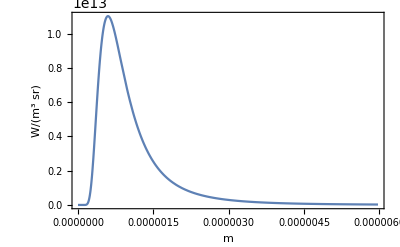

```mathematica
PlanckRadiationLaw[Quantity[4853,"Kelvins"],"SpectralPlot"]
```

## 2. What is a Safe Distance from the Balrog?

Worded another way, this question asks if its possible to engage this monster in close combat, as Gandalf does, or would an observer that is too close be at risk for spontaneous combustion. Answering this requires a calculation of the net luminosity of each part of the Balrog and a brief explanation of power absorbed from a blackbody.

## Power Absorption

A blackbody radiates in all directions, and the power received by any nearby object is a fraction of its total power. Even so, it is necessary to know that fraction. The albedo of the receiving object is also taken into account. The albedo of an object is a measurement of how it differs from a blackbody. An albedo of 1 says that all power is reflected from the surface, while an albedo of 0 says that all power is transferred by the surface into the object. This Wikipedia Article explains further. 
	As is explained in the article, the effective temperature for an object near a radiating blackbody is given by the expression below.

```mathematica
PwrIn[R_,a_, d]=(L*R^2*(1-a))/(4*d^2);
```

PwrIn is the energy received by the observer, in Watts.
L is the luminosity of the nearby blackbody, in Watts.
a is the albedo of the observer, a controlled variable.
d is the distance between the observer and the blackbody, a controlled variable. 

R proves inconsequential when determining the effective temperature, and thus the thermal measurement for an observer near a blackbody is given by the expression below.

```mathematica
obsTemp=√((L*(1-a))/(16π*σ*d^2));
```

obsTemp is the temperature of the observer, in Kelvins.
L is the luminosity of the nearby blackbody, in Watts.
a is the albedo of the observer, a controlled variable.
σ is the Stefan-Boltzmann constant, 5.67 * 10^-8 Watts/(meter^2 Kelvin^4).
d is the distance between the observer and the blackbody, a controlled variable.

## Accounting for Surface Area

Durin’s Bane is a complex shape, but only those parts that are aflame can properly be analyzed as a blackbody. The flames themselves are not measured as their surface area suggests a particle density not sufficient for spectral analysis. (*FIXME: Ensure this is worded properly *). In other words, the interest is on the source of the fire, not the fire itself.
	Thus, calculating the total surface area of the Balrog is simplified to the combination of only 3 different shapes: spheres, cylinders, and boxes.
	
	There is no consensus among fans nor is there a definite answer in the Lord of the Rings lore to clarify the dimensions of the Balrog itself, only that it is “greater” than a man. For the purposes of this project, 3 sizes of Balrog are considered: the same size of a human, larger than a human, and much larger than a human. Respectively these are called medium, large, and huge. (Yes, that is taken from D&D). Units are in meters.
	
	The radii for the medium creature are the same as for an average human male.
	The radii for the large creature increases by a factor of 1.5. 
	The radii for the huge creature increases by a factor of 2 from the large creature.
	
	It is not clear if the film version of the demon is size large or size huge from these calculation. 
	
	Because there are 3 different Balrogs, there are 3 different Luminosities, and 3 different scenarios for the observer.

```mathematica
medPwrIn[R_,a_,d_]=(L1*R^2*(1-a))/(4*d^2);
largePwrIn[R_,a_,d_] = (L2*R^2*(1-a))/(4*d^2);
hugePwrIn[R_,a_,d_]=(L3*R^2*(1-a))/(4*d^2);
```

### Spheres as Hands, Feet, and the Head

#### Medium

```mathematica
medHead=Area[Sphere[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]},r]] /. r->0.56;
medHands=2*Area[Sphere[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]},r]] /. r-> 0.17;
medFeet=2*Area[Sphere[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]},r]] /. r-> 0.25;
```

#### Large

```mathematica
largeHead=Area[Sphere[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]},r]] /. r->0.84;
largeHands=2*Area[Sphere[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]},r]] /. r->0.255;
largeFeet=2*Area[Sphere[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]},r]] /. r->0.375;
```

#### Huge

```mathematica
hugeHead=Area[Sphere[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]},r]] /. r->1.68;
hugeHands=2*Area[Sphere[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]},r]] /. r->0.51;
hugeFeet=2*Area[Sphere[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]},r]] /. r->0.75;
```

### Cylinders as Arms and Legs

```mathematica
Clear[h]
```

```mathematica
areaCylinder[r_,h_] = 2π*r*h+2π*r^2;
```

The arms and legs are considered without the joints (the elbows and the knees). The interest is in the net surface area, the bend of the limbs being negligible to the data in question.

#### Medium

```mathematica
medArms=areaCylinder[0.19,1.5];
medLegs=areaCylinder[0.0762,0.9652];
```

#### Large

```mathematica
largeArms=areaCylinder[0.285,2.25];
largeLegs=areaCylinder[0.1143,1.4478];
```

#### Huge

```mathematica
hugeArms=areaCylinder[0.57,4.5];
hugeLegs=areaCylinder[0.2286,2.8956];
```

### Rectangular Prism as a Torso and Pelvis

The torso and pelvis is considered as one large object.

```mathematica
Clear[h]
```

```mathematica
areaRectPrism[l_,w_,h_]=2*(l*w)+4*(w*h);
```

#### Medium

```mathematica
medBody=areaRectPrism[0.3556,0.1524,.5588];
```

#### Large

```mathematica
largeBody=areaRectPrism[0.5334,0.2286,0.8382];
```

#### Huge

```mathematica
hugeBody=areaRectPrism[1.0668,0.4572,1.6764];
```

### Surface Areas

```mathematica
medArea=medArms+medBody+medFeet+medHands+medHead+medLegs;
largeArea=largeArms+largeBody+largeFeet+largeHands+largeHead+largeLegs;
hugeArea=hugeArms+hugeBody+hugeFeet+hugeHands+hugeHead+hugeLegs;
```

Medium Balrog surface area: 9.20311 m^2.
Large Balrog surface area: 18.1227 m^2.
Huge Balrog surface area: 72.4909 m^2.

### Power Out

Using the Stefan-Boltzmann law, we find the power produced as well as the luminosity.

```mathematica
j=PwrOut[T]
```

3.14455×10^7

```mathematica
(3.238572161366151*^20)/(1216.51618+highLambda)^4
```

3.14419×10^7

j=3.14378 x10^7 Watts/m^2.

```mathematica
L1=Lum[medArea];
L2=Lum[largeArea];
L3=Lum[hugeArea];
```

```mathematica
Manipulate[Plot[medPwrIn[R,a, d],{R,0.2,3},PlotRange->All],{d,0.1,10,0.1},{a,0,0.99,0.01}]
```

```mathematica
Manipulate[Plot[largePwrIn[R,a, d],{R,0.2,3},PlotRange->All],{d,0.1,10,0.1},{a,0,0.99,0.01}]
```

```mathematica
Manipulate[Plot[hugePwrIn[R,a, d],{R,0.2,3},PlotRange->All],{d,0.1,10,0.1},{a,0,0.99,0.01}]
```

### Observer Temperatures

```mathematica
Manipulate[Plot[√((L1*(1-a))/(16π*σ*d^2)), {d, 0.1,5}],{a,0.1,0.9,0.1}]
```

```mathematica
Manipulate[Plot[√((L2*(1-a))/(16π*σ*d^2)), {d, 0.1,5}],{a,0.1,0.9,0.1}]
```

```mathematica
Manipulate[Plot[√((L3*(1-a))/(16π*σ*d^2)), {d, 0.1,5}],{a,0.1,0.9,0.1}]
```

## Answering Question 2

According to this webpage from the Richmond Times-Dispatch, humans cannot survive temperatures greater than 140° F.

```mathematica
UnitConvert[Quantity[140,"DegreesFahrenheit"],"Kelvins"] // N
gandalfTemp=√((L3*(0.5))/(16π*σ*d^2))/.d->BridgeAcutal (* The temperature Gandalf would be exposed to on the bridge of Khazad-Dum *)
safeDistance=(d/1000)/.Solve[√((L3*(0.5))/(16π*σ*d^2))==333.15][[2]] (* Safe distance from Durin's Bane given in km *)
```

333.15 K

6.2497×10^6

64.1611

The manipulable power-in graphs each detail the amounts of energy received by an observer based upon their distance, albedo, and size. The average surface area of an adult human is 2 m^2, which is the near center of each curve. That value at 10 meters with a 99% albedo is at a minimum 30,000 Watts in the case of the medium Balrog and a maximum of 300,000 Watts in the case of the huge Balrog. At a 90% albedo in each of the temperature graphs, the lowest heat in Kelvins is 1 million at 5 meters away. Recalling earlier that the temperature of Durin’s Bane is 83% the temperature of the sun, and the conclusion is clear: the safest distance from the Balrog is far far away. 

	An additional comment is made here. While the stuff  (be it magic, magical lava, magical blood, demon goop, or invisible gremlins) that causes the flames on the Balrog is 80% as hot as the sun, the surface of its body may not be. The material that covers the creature may be sufficiently insulated to allow interaction with the environment - after all, it doesn’t burn the ground it stands on. What has been found here may be according to the inner surface area of the Balrog. Even so, this satisfies the hypothesis.

## 3. What are analogies for the Balrog, if they exist?

## Time Travel

Having calculated the limits of the power output by this incredibly energetic monster, we can now make some references to more common objects and circumstances which allow us to gain a better understanding of what the Balrog is capable of in context. For these questions the huge Balrog is considered.

First, we consider if the Balrog could power the Delorean from Back to the Future. Though the film states that the car needs 1.21 jigowatts of energy, this is an acceptable manner of pronouncing gigawatts of energy. Since a watt is nothing more than a Joule per second, we can solve for the time that it would take the Balrog to “fuel” the Delorean for 1 second, which, according to Dr. Emmet Brown, should be enough to initiate time travel.

This website does a nice job of showing just how much of an energy hog the Delorean really is.

```mathematica
Import["https://static.wikia.nocookie.net/bttf/images/1/11/Arrival1.jpg/revision/latest/scale-to-width-down/720?cb=20080210065704"]
```

-Graphics-

```mathematica
deloreanWattage=1.21*10^9;
medSeconds=t/.Solve[t(L1/deloreanWattage)==1]
medHours=medSeconds/3600
largeSeconds=t/.Solve[t(L2/deloreanWattage)==1]
largeHours=largeSeconds/3600
hugeSeconds=t/.Solve[t(L3/deloreanWattage)==1]
hugeHours=hugeSeconds/3600
```

{4.18112}

{0.00116142}

{1.85828}

{0.000516188}

{0.464569}

{0.000129047}

The medium Balrog can power the Delorean in 4 seconds, the large one in 2, and the huge one in 0.5 seconds.

## Toast

After all of this time travel, though, surely one would be hungry and require some form of sustenance. Though Durin’s Bane could most easily discharge energy at a faster rate than a toaster, a toaster would probably do a more decent job of creating a desirable meal. An average toaster requires ~1,200 Watts during the ~2 minutes that it is toasting whatever is inside of it.

```mathematica
Import["https://m.media-amazon.com/images/I/71cahwzPu6L._AC_SL1500_.jpg",ImageSize->Small]
```

-Graphics-

```mathematica
toasterWattage=1200;
toasterRunTime=60*2;
L1/(toasterRunTime*toasterWattage)//N
L2/(toasterRunTime*toasterWattage)//N
L3/(toasterRunTime*toasterWattage)//N
```

2009.69

4521.81

18087.2

The medium Balrog can power 2009 toasters per second.
	The large Balrog can power 4521 toasters per second.
	The huge Balrog can power 18087 toasters per second.

## Home Entertainment

A typical 50” LED TV requires 100 Watts to be powered, a DVD player around 13 Watts, and a sound system that can produce 110 dB (that’s akin to a rock concert in amplitude) requires ~100 Watts. In total, if we take the wattage of Durin’s Bane, we find that in order to watch the full extended editions of BOTH The Lord of The Rings and The Hobbit series, Durin’s Bane would have to show up to the party and be hooked up to a capacitor for only ~53 seconds to allow everyone else the privilege of watching the ENTIRE FILM FRANCHISE. After that, he could leave (if he wanted to).

```mathematica
Import["https://www.essentialhome.eu/blog/wp-content/uploads/2020/05/movie-playing-on-projection-screen-in-home-theater-915093896-5bdb7eb0c9e77c0026d2970f.jpg",ImageSize->Large]
```

-Graphics-

```mathematica
TVWatts=100;
DVDWatts=13;
SoundSystemWatts=100;

(* The time, in hours, for which the Balrog could power this home theater system in ONE SECOND *)

medOneSecondPower=(L1/(TVWatts+DVDWatts+SoundSystemWatts))/3600//Round
largeOneSecondPower=(L2/(TVWatts+DVDWatts+SoundSystemWatts))/3600//Round
hugeOneSecondPower=(L3/(TVWatts+DVDWatts+SoundSystemWatts))/3600//Round 

(* Technically, the total runtime is only 20 hours and 18 minutes, but between getting snacks and changing DVDs, we figured an additional 12 minutes was a reasonable addition *)

totalRuntime=20.5//N; 

totalRuntime/medOneSecondPower
totalRuntime/largeOneSecondPower
totalRuntime/hugeOneSecondPower
```

377

849

3397

0.0543767

0.0241461

0.00603474

The medium Balrog can power the home theater system for 377 hours in 0.054 seconds.
	The large Balrog can power the home theater system for 849 hours in 0.024 seconds.
	The huge Balrog can power the home theater system for 3397 hours in 0.006 seconds.

## Driving a Car

If a Balrog could be connected to a motor vehicle (internal combustion or electric), how far could such a vehicle go in 1 hour?

```mathematica
(* Watts are 1 joule per 1 second *)
medJoules=L1*3600;
largeJoules=L2*3600;
hugeJoules=L3*3600;
```

```mathematica
(* Initial velocity is 0 *)
m=1240; (*Mass of vehicle in kg*)
```

```mathematica
(* Velocities in meters/second *)
medVel=√((2*medJoules)/m)
largeVel=√((2*largeJoules)/m)
hugeVel=√((2*hugeJoules)/m)
```

40992.2

61488.4

122977.

```mathematica
medDist=(medVel*3600)/1000
largeDist=(largeVel*3600)/1000
hugeDist=(hugeVel*3600)/1000
```

147572.

221358.

442716.

```mathematica
UnitConvert[Quantity[medDist, "Kilometers"],"Miles"]
UnitConvert[Quantity[largeDist, "Kilometers"],"Miles"]
UnitConvert[Quantity[hugeDist, "Kilometers"],"Miles"]
```

91697. mi

137546. mi

275091. mi

The medium Balrog raises the car to speeds of 41000 m/s.
	The large Balrog raises the car to speeds of 61.500 m/s.
	The huge Balrog raises the car to speeds of 123000 m/s. 
	
	The medium Balrog will move the car 147572 kilometers or 91697 miles in one hour.
	The large Balrog will move the car 221358 kilometers or137546 miles in one hour.
	The huge Balrog will move the car 442716 kilometers 275091 miles in one hour.
	
	These are all faster than the speed of sound! Indeed, these speeds approach the speed of light!

## Conclusion

## Hypothesis

The hypothesis proved false in every instance. Not only is Durin’s Bane much hotter than originally anticipated, it is much more dangerous and possesses exponentially more amounts of energy than molten rock or molten metal. Blackbody analysis suggests that temperatures on Durin’s Bane approach that of the sun. The Luminosity discovered proves the danger of proximity. Analogies for these data exist, and enable imagination to flourish for some.

Perhaps one day mankind will tap into fusion power and have machines whose internals mimic that of Durin’s Bane. Until then, the conclusion of this experiment disproves of the hypothesis that the Balrog is warm and safe.